```mathematica
DSolveValue[{u''[x]+u[x]==x, u[0]==1, u[1]==3},u[x],x]
```

x+Cos[x]-Cot[1] Sin[x]+2 Csc[1] Sin[x]

```mathematica
(* Исходные данные *)
```

```mathematica
(* Решение задачи:
1 - метод Бубнова - Галеркина;
  2 - метод Галеркина;
  3 - МНК; *)
(* Учет ГУ:
1 - метод штрафов;
  2 - метод множителей Лагранжа;
*)
```

```mathematica
method = 1; order = 3;
```

```mathematica
a=0;
b=1;
A[ϕ_,x_]:=D[ϕ,{x,2}]+ϕ;
F[x_]:=-x;
ϕi[x_,i_]:=(x+1)^i;
isLagrange = True;
isPenalty = True;
```

```mathematica
conditions = {{a, 1,1 }, {b,0, 3}} ;(*{Point, Derivative, Value}*)
weightBoundaryEq[x_,i_, j_,k_, weight_] := weight*(D[ϕi[z, i], {z, k}]/.z->x)*(D[ϕi[z, j], {z, k}]/.z->x);
weightBoundaryEqRight[x_,y_,i_, k_, weight_] := y*weight*(D[ϕi[z, i], {z, k}]/.z->x);
lagrangeBoundaryEq[x_, i_, k_, λ_] := λ*(D[ϕi[z, i], {z, k}]/.z->x);
```

```mathematica
(* Функции *)
```

```mathematica
equation[] := Module [ {C,ψ,eq,eqRight},
C=Table[Subscript[c, i],{i,1,order}];
Switch[method,
1,
ψ=Table[ϕi[x,i],{i,1,order}],
2,
ψ=Table[(x-1/2)^(i-1),{i,1,order}],
3,
ψ=Table[A[ϕi[x,i],x],{i,1,order}]
];
eq=Table[∑_(i=1)^order C⟦i⟧∫_a^b A[ϕi[x,i],x]ψ⟦j⟧ⅆx,{j,1,order}];
eqRight=Table[∫_a^b F[x]ψ⟦j⟧ⅆx,{j,1,order}];
Return[{C, eq, eqRight}];
];
penaltyBoundary[{C_, equation_, right_}, weight_] := Module[{solA,numSol,eq = equation, eqRight = right },
eq+=Table[∑_(i=1)^order C⟦i⟧∑_(l=1)^2 weightBoundaryEq[conditions⟦l, 1⟧, i, j, conditions⟦l,2⟧, weight], {j, 1, order}];
eqRight+=Table[∑_(l=1)^2 weightBoundaryEqRight[conditions⟦l, 1⟧,conditions⟦l, 3⟧, j, conditions⟦l, 2⟧, weight],{j,1,order}];
solA=First@Solve[eq==eqRight,C];
numSol[x_]:=∑_(i=1)^order C⟦i⟧ϕi[x,i]/.solA;
Return[{C/.solA,numSol[x]}];
];
lagrangeBoundary[{C_, equation_, right_}] := Module[{solA,numSol,coefLagr,eq = equation, eqRight = right},
coefLagr=Table[Subscript[λ, i],{i,0,1}];
eq += Table[∑_(l=1)^2 lagrangeBoundaryEq[conditions⟦l, 1⟧,j,conditions⟦l, 2⟧,coefLagr⟦l⟧], {j, 1, order}];
eq=eq~Join~Table[∑_(i=1)^order C⟦i⟧(D[ϕi[x,i],{x,conditions⟦l, 2⟧}]/.x->conditions⟦l, 1⟧),{l,1,2}];
eqRight=eqRight~Join~Table[conditions⟦l, 3⟧,{l, 1, 2}];
solA=Solve[eq==eqRight,C~Join~coefLagr]⟦1⟧;
solA=solA⟦1;;-1-Length[coefLagr]⟧;
numSol[x_]:=∑_(i=1)^order C⟦i⟧ϕi[x,i]/.solA;
Return[{C/.solA,numSol[x]}];
];
```

```mathematica
aa[x_]=Last@lagrangeBoundary[equation[]]
```

-(8501 (1+x))/1167+(52007 (1+x)^2)/4668-(4445 (1+x)^3)/1556

```mathematica
printResult[penalty_,lagrange_]:=Module[{analSol,i,C,numSol,δ,tableFraction,tableNum,tableErr,M, result, plots, temp},
result={};
tableNum = {};
tableErr = {};
plots = {};
temp = DSolve[{A[u[ξ],ξ]==F[ξ],u'[a]==conditions⟦1,3⟧,u[b]==conditions⟦2, 3⟧},u[ξ],ξ]⟦1,1,2⟧/.ξ->x;
analSol[x_]:=temp;
AppendTo[plots, Plot[analSol[x], {x, a, b}, PlotStyle->{Black, Dashed, Thick}, PlotLegends->{"Analytical"}]];
M={1, 10, 1000, 10000}; 
GraphColors={Red, Green, Purple, Yellow};
presition = 3;
For[i=1, i <= Length@M, ++i,
If[penalty,
{C, numSol[x_]}= penaltyBoundary[equation[], M[[i]]];
δ=N@Sqrt@(Integrate[(analSol[x]-numSol[x])^2,{x,a,b}]/Integrate[(analSol[x])^2,{x,a,b}]);
AppendTo[result,{C,numSol[x],δ}];
AppendTo[plots, Plot[numSol[x], {x, a, b}, PlotStyle->{GraphColors[[i]],Thick}, PlotLegends->{StringJoin["Penalty = ", ToString@M[[i]]]}]];
AppendTo[tableNum, {SetAccuracy[N@C, presition] , StringJoin["Penalty = ", ToString@M[[i]]]}];
AppendTo[tableErr, {SetAccuracy[δ, presition], StringJoin["Penalty = ", ToString@M[[i]]]}];
];
];
If[lagrange,
{C, numSol[x_]}= lagrangeBoundary[equation[]];
δ=N@Sqrt@(Integrate[(analSol[x]-numSol[x])^2,{x,a,b}]/Integrate[(analSol[x])^2,{x,a,b}]);
AppendTo[result,{C,numSol[x],δ}];
AppendTo[plots, Plot[numSol[x], {x, a, b}, PlotStyle->{Blue, Thick}, PlotLegends->{"Lagrange"}]];
AppendTo[tableNum, {SetAccuracy[N@C, presition], "Lagrange"}];
AppendTo[tableErr, {SetAccuracy[δ, presition], "Lagrange"}];
];
Print[tableNum];
Print[tableErr];
Return@plots;
]
```

```mathematica
resPlots = printResult[isPenalty, isLagrange];
```

{{{-7.89,10.09,-2.44},Penalty = 1},{{-7.36,11.02,-2.81},Penalty = 10},{{-7.29,11.14,-2.86},Penalty = 1000},{{-7.28,11.14,-2.86},Penalty = 10000},{{-7.28,11.14,-2.86},Lagrange}}

{{0.4,Penalty = 1},{0.07,Penalty = 10},{0.03,Penalty = 1000},{0.03,Penalty = 10000},{0.03,Lagrange}}

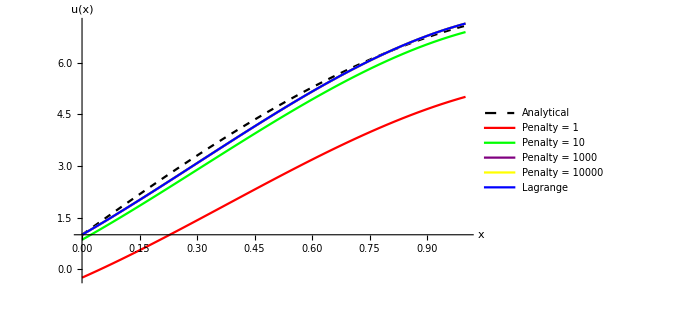

```mathematica
Show[resPlots,AxesLabel->{"x","u(x)"},PlotRange->All, ImageSize-> 500]
```